## Parabolic x, xmax =1 (Constant effective mass)

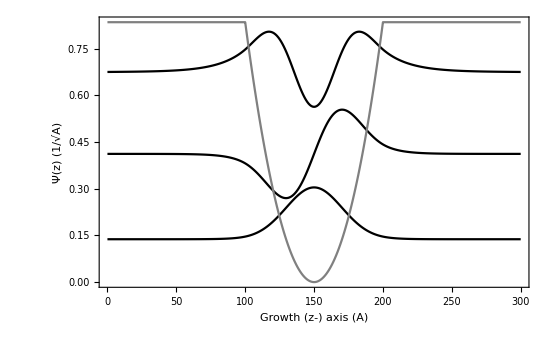

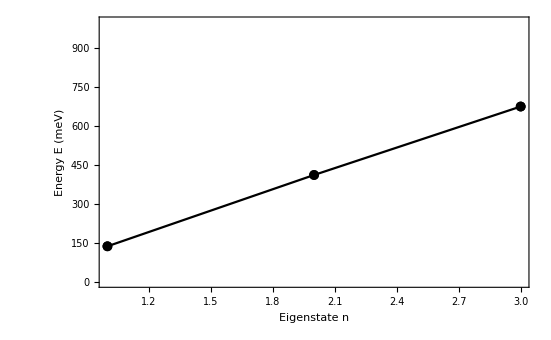

```mathematica
ClearAll["Global`*"]

hom=7.62559/0.067;(*ℏ^2/m^* for GaAs in eV A^2*)
dz=1.;zmin=0.;zmax=300.;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
xmin=0;xmax=1;a=100;b=100;
x=xmin+(xmax-xmin)*(z-(b+a/2))^2/(a/2)^2;
Do[If[z⟦i⟧<100||z⟦i⟧>200,x⟦i⟧=1.],{i,lz}]
v=0.67*1.247x;
c=-0.5*hom/dz^2;b=hom/dz^2+v;

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c};
Do[H⟦i,{i-1,i,i+1}⟧= {c,b⟦i⟧,c},{i,2,lz-1}]
ψ=Eigenvectors[H]⟦-Range[3]⟧;
energy=Eigenvalues[H]⟦-Range[3]⟧;
plot={0.,0.,0.,0.};
Do[
plot⟦j⟧=ListLinePlot[Table[{z⟦i⟧,ψ⟦j,i⟧+energy⟦j⟧},{i,lz}],PlotStyle->Black,Frame->True, FrameLabel->{"Growth (z-) axis (A)","Ψ(z) (1/√A)"},PlotRange->All]
,{j,3}];
plot⟦4⟧=ListLinePlot[Table[{z⟦i⟧,v⟦i⟧},{i,lz}],PlotStyle->Gray,Frame->True, FrameLabel->{"Growth (z-) axis (A)","Ψ(z) (1/√A)"},PlotRange->All];
energyplot=ListPlot[1000*energy,Joined-> True,Mesh->Full,PlotStyle->Black,PlotRange->{{1,3},{0,1000}},Frame->True, FrameLabel->{"Eigenstate n","Energy E (meV)"}];
Show[plot,PlotRange->All]
Show[energyplot]
```

## Parabolic x energies (Constant effective mass)

```mathematica
ClearAll["Global`*"]

hom=7.62559/0.067;(*ℏ^2/m^* for GaAs in eV A^2*)
dz=1.;zmin=0.;zmax=300.;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
xmin=0;xmax=10;a=100;b=100;
x=xmin+(xmax-xmin)*(z-(b+a/2))^2/(a/2)^2;
Do[If[z⟦i⟧<100||z⟦i⟧>200,x⟦i⟧=xmax],{i,lz}]
v=0.67*1.247x;
c=-0.5*hom/dz^2;b=hom/dz^2+v;

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c};
Do[
H⟦i,{i-1,i,i+1}⟧= {c,b⟦i⟧,c};
,{i,2,lz-1}]
energy=Eigenvalues[H]⟦-Range[10]⟧;
erel=energy/(2energy⟦1⟧);
Grid[Prepend[Table[{i,1000*energy⟦i⟧,erel⟦i⟧},{i,1,10}],{"State index, n","Eigenvalue E_n(meV)","E_n/(2E_1)"}],Frame->All]
```

State index, n | Eigenvalue E_n(meV) | E_n/(2E_1)
1 | 435.89 | 0.5
2 | 1307.25 | 1.49952
3 | 2177.78 | 2.49808
4 | 3047.46 | 3.49567
5 | 3916.28 | 4.49228
6 | 4784.1 | 5.48774
7 | 5650.26 | 6.48129
8 | 6511.83 | 7.46958
9 | 7357.14 | 8.43921
10 | 8131.43 | 9.32739

## Poschl-Teller Potential

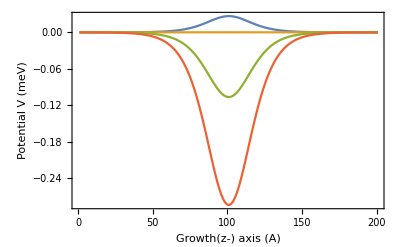

```mathematica
dz=1.;zmin=-100.;zmax=100.;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
α=0.05;λ={0.75,1.0,1.5,2.0};v=0.*λ;
Do[v⟦i⟧=-hom/2*α^2*(λ⟦i⟧(λ⟦i⟧-1))/Cosh[α*z]^2,{i,Length[v]}]
ListLinePlot[v,PlotRange->All,Frame->True, FrameLabel->{"Growth(z-) axis (A)","Potential V (meV)"}]
```

## Poschell (Constant effective mass)

```mathematica
ClearAll["Global`*"]
hom=7.62559/0.067;(*ℏ^2/m^* for GaAs in eV A^2*)
dz=1.;zmin=-100.;zmax=100.;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
α=0.05;λ={1.5,2.0,5.0,10.};v=λ*0;energy=ConstantArray[{0,0},Length[λ]];
Do[v⟦i⟧=-hom/2*α^2*(λ⟦i⟧(λ⟦i⟧-1))/Cosh[α*z]^2;
c=-0.5*hom/dz^2;b=hom/dz^2+v⟦i⟧;

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c};
Do[
H⟦i,{i-1,i,i+1}⟧= {c,b⟦i⟧,c};
,{i,2,lz-1}];
If[Sort[Eigenvalues[H]]⟦1⟧<0,energy⟦i,1⟧=10^3*Sort[Eigenvalues[H]]⟦1⟧,energy⟦i,1⟧="-"];
If[Sort[Eigenvalues[H]]⟦2⟧<0,energy⟦i,2⟧=10^3*Sort[Eigenvalues[H]]⟦2⟧,energy⟦i,2⟧="-"];
,{i,Length[λ]}]
Grid[Prepend[Table[{λ⟦i⟧,energy⟦i,1⟧,energy⟦i,2⟧},{i,Length[λ]}],{"λ","E_1(meV)","E_2(meV)"}],Frame->All]
```

λ | E_1(meV) | E_2(meV)
1.5 | -34.3316 | -
2. | -142.236 | -
5. | -2276.6 | -1281.45
10. | -11525.4 | -9112.36

## Constant Effective mass well Convergence test

```mathematica
ClearAll["Global`*"]
hom=7.62559/0.067;
n={1,2,5,10,20};
dz=1/n;zmin=-150.;zmax=150.;
energy=0*dz;
Do[
z=Range[zmin,zmax,dz⟦j⟧];lz=Length[z];i0=(Length[z]+1.)/2.;
α=0.05;λ=5;
v=-hom/2*α^2*(λ(λ-1))/Cosh[α*z]^2;
c=-0.5*hom/dz⟦j⟧^2;b=hom/dz⟦j⟧^2+v;

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c};
Do[H⟦i,{i-1,i,i+1}⟧= {c,b⟦i⟧,c},{i,2,lz-1}];
energy⟦j⟧= Sort[Eigenvalues[H]]⟦{1,2}⟧
,{j,Length[dz]}]
Grid[Prepend[Table[{n⟦i⟧,1000*energy⟦i,1⟧,1000*energy⟦i,2⟧},{i,Length[dz]}],{"N(A^-1)","E_1 (meV)","E_2 (meV)"}],Frame->All]
```

N(A^-1) | E_1 (meV) | E_2 (meV)
1 | -2276.6 | -1281.45
2 | -2276.37 | -1280.68
5 | -2276.31 | -1280.46
10 | -2276.3 | -1280.43
20 | -2276.3 | -1280.42

## Variable Effective mass

```mathematica
(*Concentration*)
xmax=0.2;
well=Join[Range[20.,120.,20.],{160,200}];barrier=100;
energy=ConstantArray[{0.,0.},Length[well]];
Do[
dz=1.;zmin=0.;zmax=2.*barrier+well⟦j⟧;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
x=ConstantArray[xmax,lz];
Do[If[z⟦i⟧>barrier&&z⟦i⟧<barrier + well⟦j⟧,x⟦i⟧=0.],{i,lz}];
v=0.67*1.247x;

(*Effective mass*)
m=(0.067+0.083x);
Do[m⟦i⟧=0.5*(m⟦i⟧+m⟦i+1⟧),{i,2,lz-1}];
hom=7.62559/m;

c=-0.5*hom/dz^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-2⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];

If[Sort[Eigenvalues[H]]⟦1⟧<Max[v],energy⟦j,1⟧=10^3*Sort[Eigenvalues[H]]⟦1⟧,energy⟦j,1⟧="-"];
If[Sort[Eigenvalues[H]]⟦2⟧<Max[v],energy⟦j,2⟧=10^3*Sort[Eigenvalues[H]]⟦2⟧,energy⟦j,2⟧="-"];
,{j,Length[well]}]
Grid[Prepend[Table[{well⟦i⟧,energy⟦i,1⟧,energy⟦i,2⟧},{i,Length[well]}],{"well(A)","E_1 (meV)","E_2 (meV)"}],Frame->All]
```

well(A) | E_1 (meV) | E_2 (meV)
20. | 129.304 | -
40. | 81.9128 | -
60. | 54.3012 | -
80. | 38.2402 | 139.387
100. | 28.2855 | 107.973
120. | 21.737 | 84.6217
160 | 13.9637 | 55.2022
200 | 9.71386 | 38.6145

## Variable Effective mass well Convergence test

```mathematica
(*Concentration*)
xmax=0.75;
well=20.;barrier=100;
n=Range[2.,12.,2.];dz=1./n;
energy=0*dz;
Do[
zmin=0.;zmax=2.*barrier+well;
z=Range[zmin,zmax,dz⟦j⟧];lz=Length[z];i0=(Length[z]+1.)/2.;
x=ConstantArray[xmax,lz];
Do[If[z⟦i⟧>barrier&&z⟦i⟧<barrier + well,x⟦i⟧=0.],{i,lz}];
v=0.67*1.247x;

(*Effective mass*)
m=(0.067+0.083x);
Do[m⟦i⟧=0.5*(m⟦i⟧+m⟦i+1⟧),{i,2,lz-1}];
hom=7.62559/m;

c=-0.5*hom/dz⟦j⟧^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz⟦j⟧^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz⟦j⟧^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz⟦j⟧^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-2⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];

energy⟦j⟧=Eigenvalues[H]⟦-1⟧;
,{j,Length[dz]}]

Grid[Prepend[Table[{n⟦i⟧,10^3 energy⟦i⟧},{i,Length[n]}],{"N(A^-1)","E_1 (meV)"}],Frame->All]
```

N(A^-1) | E_1 (meV)
2. | 276.857
4. | 273.856
6. | 272.856
8. | 272.355
10. | 272.055
12. | 271.854

## Lowest two states: Double quantum well

## Decreasing Barrier width:

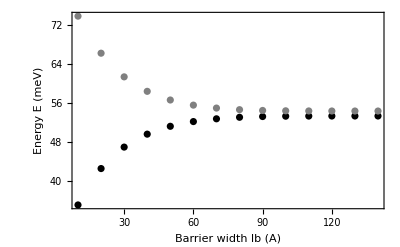

```mathematica
(*Concentration*)
xmax=0.2;
well=60.;barrierout=200.;barrierin=Range[10,140,10];
nwells = 2;
energy=ConstantArray[{0.,0.},Length[barrierin]];
dz=1.;
Do[
zmin=0.;zmax=2.*barrierout+barrierin⟦j⟧*(nwells-1)+nwells*well;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
x=ConstantArray[xmax,lz];
Do[If[z⟦i⟧>zmin+barrierout&&z⟦i⟧<zmax-barrierout ,
l=Mod[z⟦i⟧- barrierout,well+barrierin⟦j⟧];
If[l< well,x⟦i⟧=0.]]
,{i,lz}];
v=0.67*1.247x;

(*Effective mass*)
m=(0.067+0.083x);
Do[m⟦i⟧=0.5*(m⟦i⟧+m⟦i+1⟧),{i,2,lz-1}];
hom=7.62559/m;

c=-0.5*hom/dz^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-2⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];

{e1,e2}=Sort[Eigenvalues[H]]⟦{1,2}⟧;
If[e1<Max[v],energy⟦j,1⟧=10^3*e1,energy⟦j,1⟧="-"];
If[e2<Max[v],energy⟦j,2⟧=10^3*e2,energy⟦j,2⟧="-"];
,{j,Length[barrierin]}];


plot1=ListPlot[Table[{barrierin⟦i⟧,energy⟦i,1⟧},{i,Length[barrierin]}],PlotStyle-> Black,PlotRange->All,Frame->True,FrameLabel->{"Barrier width lb (A)","Energy E (meV)"}];
plot2=ListPlot[Table[{barrierin⟦i⟧,energy⟦i,2⟧},{i,Length[barrierin]}],PlotStyle-> Gray,PlotRange->All,Frame->True,FrameLabel->{"Barrier width l_b (A)","Energy E (meV)"}];
Show[plot1,plot2,PlotRange-> All]
```

## Ground and First exited state of Double quantum well

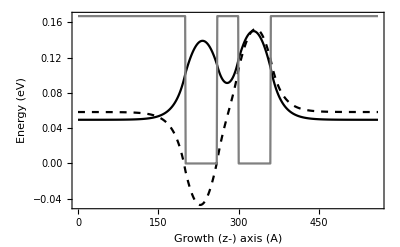

```mathematica
(*Concentration*)
xmax=0.2;
well=60.;barrierout=200.;barrierin=40;
nwells = 2;
dz=1.;zmin=0.;zmax=2.*barrierout+barrierin*(nwells-1)+nwells*well;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
x=ConstantArray[xmax,lz];
Do[If[z⟦i⟧>zmin+barrierout&&z⟦i⟧<zmax-barrierout ,
l=Mod[z⟦i⟧- barrierout,well+barrierin];
If[l<well,x⟦i⟧=0.]]
,{i,lz}];
v=0.67*1.247x;

(*Effective mass*)
m=(0.067+0.083x);
Do[m⟦i⟧=0.5*(m⟦i⟧+m⟦i+1⟧),{i,2,lz-1}];
hom=7.62559/m;

c=-0.5*hom/dz^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-2⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];

ψ=Eigenvectors[H]⟦{-1,-2}⟧;
energy=Eigenvalues[H]⟦{-1,-2}⟧;

plot1=ListLinePlot[Table[{z⟦i⟧,ψ⟦1,i⟧+energy⟦1⟧},{i,lz}],PlotStyle-> Black,PlotRange->All,Frame->True,FrameLabel->{"Growth (z-) axis (A)","Energy (eV)"}];
plot2=ListLinePlot[Table[{z⟦i⟧,ψ⟦2,i⟧+energy⟦2⟧},{i,lz}],PlotStyle-> {Black,Dashed},PlotRange->All,Frame->True,FrameLabel->{"Growth (z-) axis (A)","Energy (eV)"}];
potentialplot=ListLinePlot[Table[{z⟦i⟧,v⟦i⟧},{i,lz}],PlotStyle-> Gray,PlotRange->All,Frame->True,FrameLabel->{"Growth (z-) axis (A)","Energy (eV)"}];
Show[plot1,plot2,potentialplot,PlotRange-> All]
```

## Kroning-Penny using multiple quantum dot

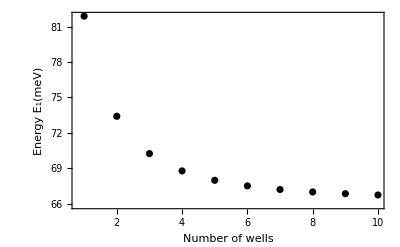

```mathematica
(*Concentration*)
xmax=0.2;
well=40.;barrierout=200.;barrierin=40;
nwells = Range[1,10];
dz=1.;zmin=0.;
energy=0.*nwells;
Do[
zmax=2.*barrierout+barrierin*(nwells⟦j⟧-1)+nwells⟦j⟧*well;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
x=ConstantArray[xmax,lz];
Do[If[z⟦i⟧>zmin+barrierout&&z⟦i⟧<zmax-barrierout ,
l=Mod[z⟦i⟧- barrierout,well+barrierin];
If[l<well,x⟦i⟧=0.]]
,{i,lz}];
v=0.67*1.247x;

(*Effective mass*)
m=(0.067+0.083x);
Do[m⟦i⟧=0.5*(m⟦i⟧+m⟦i+1⟧),{i,2,lz-1}];
hom=7.62559/m;

c=-0.5*hom/dz^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-1⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];

energy⟦j⟧=Eigenvalues[H]⟦-1⟧;
,{j,Length[nwells]}]

plot=ListPlot[Table[{nwells⟦i⟧,1000*energy⟦i⟧},{i,Length[nwells]}],PlotStyle-> Black,PlotRange->All,Frame->True,FrameLabel->{"Number of wells","Energy E_1(meV)"}]
```

## Superlattice and Multiple quantum well

```mathematica
(*Concentration*)
plot=potentialplot={0.,0.};

xmax={0.2,0.4};
well={40.,100.};barrierout={200.,100.};barrierin={40.,100.};
nwells = {10,5};
dz=1.;zmin=0.;
Do[
zmax=2.*barrierout⟦j⟧+barrierin⟦j⟧*(nwells⟦j⟧-1)+nwells⟦j⟧*well⟦j⟧;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
x=ConstantArray[xmax⟦j⟧,lz];
Do[If[z⟦i⟧>zmin+barrierout⟦j⟧&&z⟦i⟧<zmax-barrierout⟦j⟧ ,
l=Mod[z⟦i⟧- barrierout⟦j⟧,well⟦j⟧+barrierin⟦j⟧];
If[l<well⟦j⟧,x⟦i⟧=0.]]
,{i,lz}];
v=0.67*1.247x;

(*Effective mass*)
m=(0.067+0.083x);
Do[m⟦i⟧=0.5*(m⟦i⟧+m⟦i+1⟧),{i,2,lz-1}];
hom=7.62559/m;

c=-0.5*hom/dz^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-2⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];

ψ=Eigenvectors[H]⟦-1⟧;
energy=Eigenvalues[H]⟦-1⟧;

plot⟦j⟧=ListLinePlot[Table[{z⟦i⟧,2ψ⟦i⟧+energy},{i,lz}],PlotStyle-> Black,PlotRange->All,Frame->True,FrameLabel->{"Growth (z-) axis (A)","Energy (eV)"}];

potentialplot⟦j⟧=ListLinePlot[Table[{z⟦i⟧,v⟦i⟧},{i,lz}],PlotStyle-> Gray,PlotRange->All,Frame->True,FrameLabel->{"Growth (z-) axis (A)","Energy (eV)"}];
,{j,2}];

plot⟦2⟧=ListLinePlot[Table[{z⟦i⟧,5ψ⟦i⟧+energy},{i,lz}],PlotStyle-> Black,PlotRange->All,Frame->True,FrameLabel->{"Growth (z-) axis (A)","Energy (eV)"}];
```

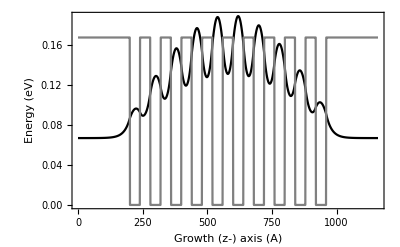

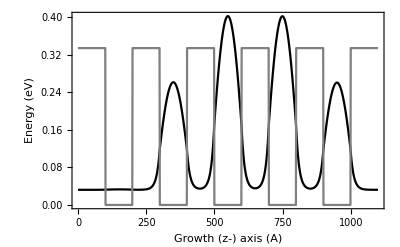

```mathematica
Show[plot⟦1⟧,potentialplot⟦1⟧,PlotRange->All]
Show[plot⟦2⟧,potentialplot⟦2⟧,PlotRange->All]
```